# BHCoordinates package

## by Ian Hinder

## Initialisation

```mathematica
<<"BHCoordinates.m"
```

## Documentation

The BHCoordinates package contains functions for analysing the coordinate locations of black holes.

### Note

In fact, these functions can be used with output from either PunctureTracker or MinTracker, and the latter could be used to track neutron stars, so the package is named too restrictively.

## Examples

```mathematica
run="D6q1_1a";
```

### BH Trajectories

```mathematica
traj0=ReadBHTrajectory[run,0];
```

```mathematica
Take[traj0,10]
```

{{3,0},{2.99977,0.00514429},{2.99835,0.034876},{2.99577,0.0824581},{2.99226,0.138325},{2.98801,0.196708},{2.98306,0.254795},{2.97752,0.312379},{2.97142,0.369961},{2.96461,0.427684}}

```mathematica
traj1=ReadBHTrajectory[run,1];
```

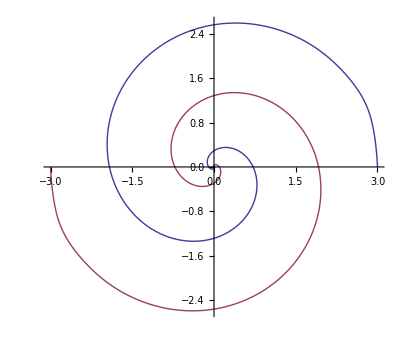

```mathematica
ListLinePlot[{traj0,traj1},PlotRange->All,AspectRatio->Automatic]
```

Separation of the BHs (radius of relative orbit)

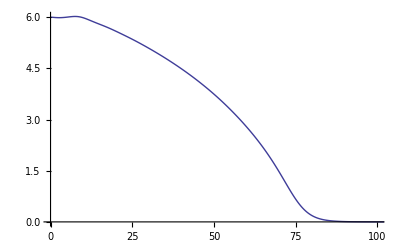

```mathematica
ListLinePlot[ReadBHSeparation[run],PlotRange->{{0,100},All}]
```

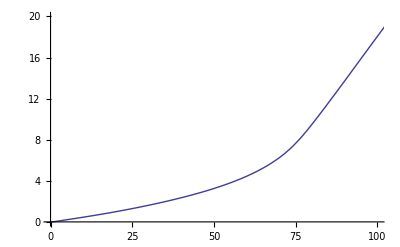

```mathematica
ListLinePlot[ReadBHPhase[run],PlotRange->{{0,100},{0,20}}]
```

### Individual coordinates

```mathematica
bh0x=ReadBHCoordinate[run,0,1]
```

DataTable[...]

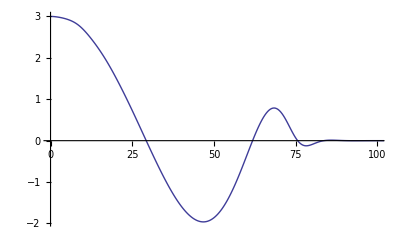

```mathematica
ListLinePlot[bh0x,PlotRange->{{0,100},All}]
```